```mathematica
numbers={a->1.,ν->0.07453,α->0.000002};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Загрузки\Диплом\Diploma_Nb

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogLinearPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier",FontSize->12, Bold},ImageSize->500,PlotStyle->{Red,PointSize[0.01]}];
```

```mathematica
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, -1}],{1,Length[x]/2+1}]]
```

```mathematica
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/Length[x],{b,0,Length[x]-1}]
```

```mathematica
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

```mathematica
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[NumPlace[x]-4;;NumPlace[x]+4]],AbsFourier[x][[NumPlace[x]-4;;NumPlace[x]+4]]}],FrameLabel->{"ν","A, mm"}]
FullPlot[x_]:=ListPlot[Transpose[{FreqList[x][[1;;Length[x]/2+1]],AbsFourier[x]}],FrameLabel->{"ν","A, mm"}]
```

N = 128

```mathematica
sig100=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,128}];
```

0.078125

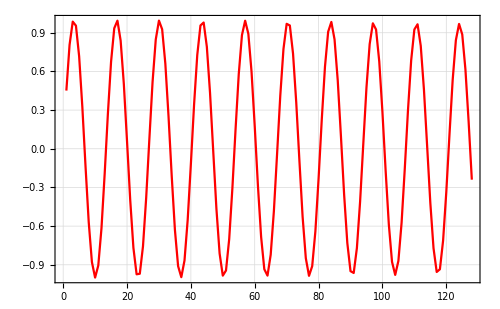

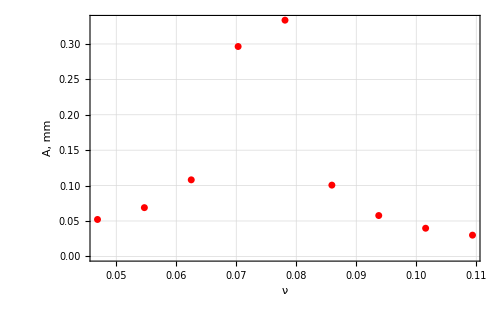

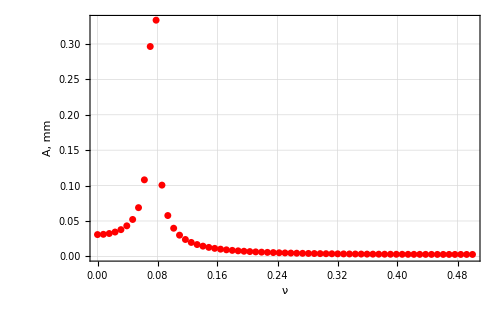

```mathematica
Freq100 =Freq[sig100]
Image100=ListLinePlot[sig100]
Fourier100=TruePlot[sig100]
FourierFull100=FullPlot[sig100]
```

N = 256

```mathematica
sig500=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,256}];
```

0.0742188

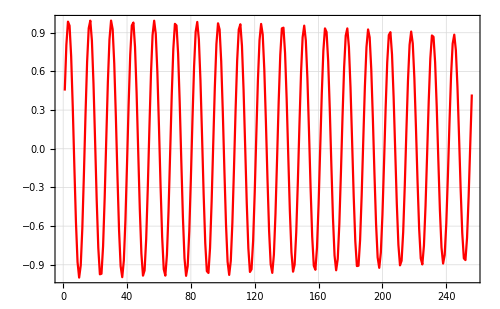

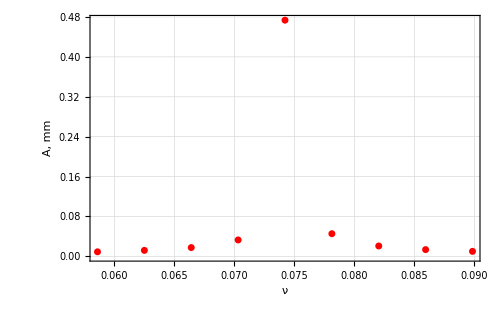

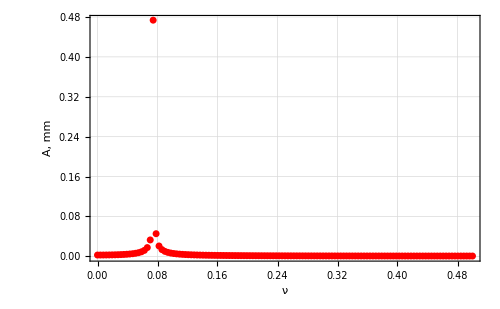

```mathematica
Freq500 =Freq[sig500]
Image500=ListLinePlot[sig500]
Fourier500=TruePlot[sig500]
FourierFull500=FullPlot[sig500]
```

N = 512

0.0742188

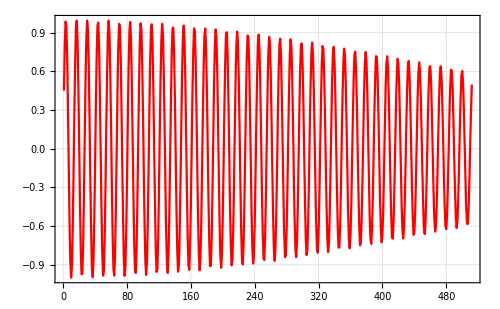

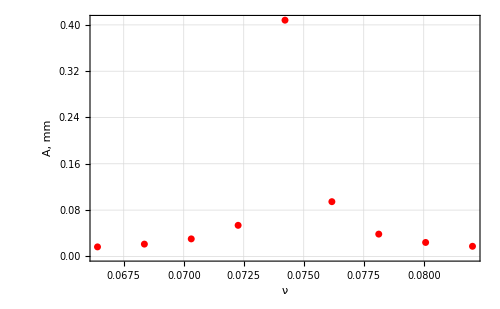

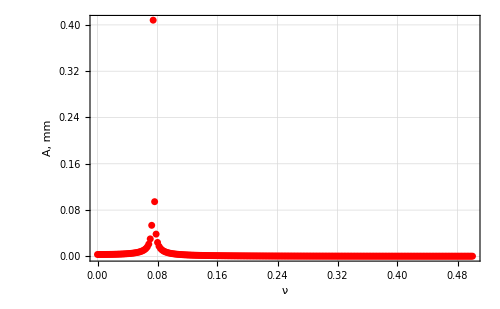

```mathematica
sig1000=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,512}];
Freq1000 =Freq[sig1000]
Image1000=ListLinePlot[sig1000]
Fourier1000=TruePlot[sig1000]
FourierFull1000=FullPlot[sig1000]
```

N = 1024

0.0742188

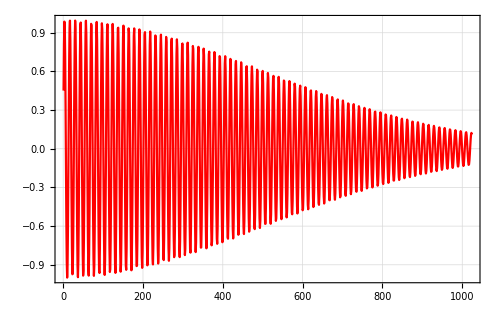

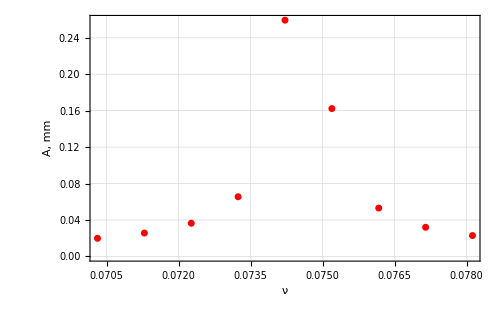

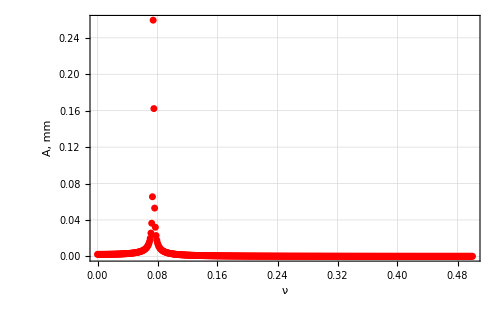

Fourier15024.png

```mathematica
sig1500=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,1024}];
Freq1500 =Freq[sig1500]
Image1500=ListLinePlot[sig1500]
Fourier1500=TruePlot[sig1500]
FourierFull1500=FullPlot[sig1500]
Export["Fourier15024.png",Fourier1500]
```

N = 4096

0.0744629

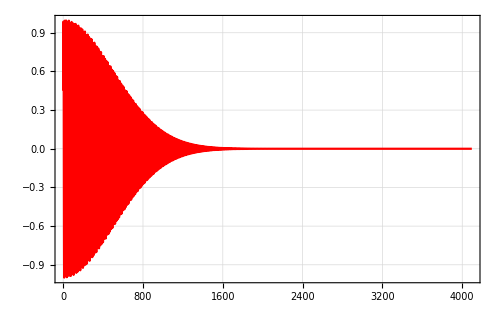

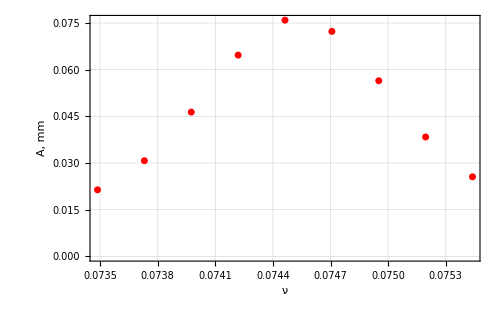

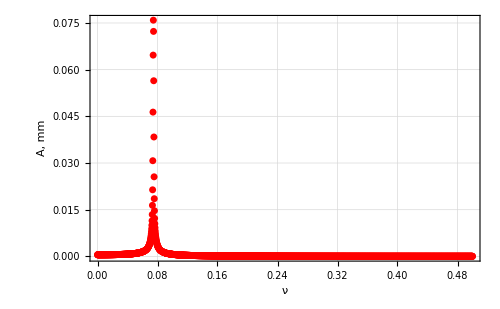

```mathematica
sig3000=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,4096}];
Freq3000 =Freq[sig3000]
Image3000=ListLinePlot[sig3000]
Fourier3000=TruePlot[sig3000]
FourierFull3000=FullPlot[sig3000]
```

```mathematica
depen =Transpose[{{128,256,512,1024,4096},{Freq100*1000, Freq500*1000,Freq1000*1000,Freq1500*1000,Freq3000*1000}-ν*1000}/.numbers]
```

{{128,3.595},{256,-0.31125},{512,-0.31125},{1024,-0.31125},{4096,-0.0671094}}

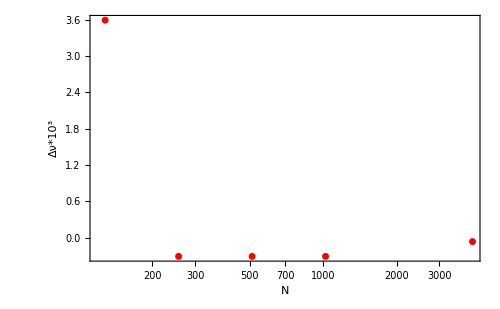

```mathematica
DeltaFourier=ListLogLinearPlot[depen,Axes->True,FrameLabel->{"N","Δν*10^3"}]
```

```mathematica
Export["DeltaFourier.png",DeltaFourier]
```

DeltaFourier.png